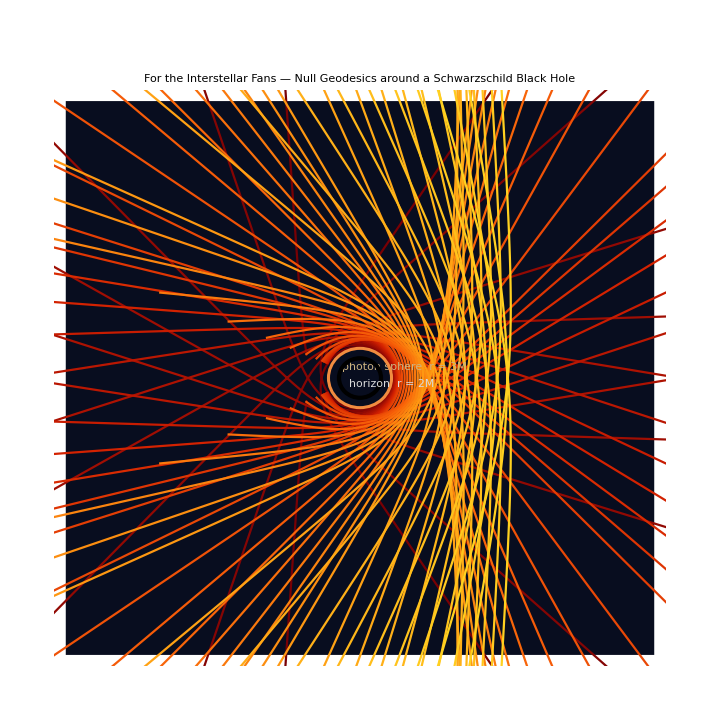

```mathematica
(*Units:G=c=1. Metric on the equatorial plane θ=π/2:ds^2=-(1-2M/r) dt^2+(1-2M/r)^(-1) dr^2+r^2 dφ^2. Null orbits reduce to the classic equation for u(φ)=1/r(φ):u''+u=3 M u^2,with closest approach at φ=0 given by u(0)=1/r_min,u'(0)=0.*)(*----------knobs students can play with----------*)ClearAll[M,rH,rPh];
M=1.0;             (*black-hole mass*)
rH=2.0 M;          (*horizon radius*)
rPh=3.0 M;          (*photon sphere*)

(*Map “how close we skim the hole” to impact parameter (for reference in class)*)
bFromRmin[rmin_]:=rmin/Sqrt[1-2 M/rmin];   (*b^2=r_min^2/(1-2M/r_min)*)

(*----------solve u''+u=3Mu^2 once per chosen r_min----------*)
ClearAll[solveU];
solveU[rmin_,φmax_:9.]:=Module[{u},NDSolveValue[{u''[φ]+u[φ]==3.0 M u[φ]^2,u[0]==1.0/rmin,u'[0]==0.0},u,{φ,-φmax,φmax},MaxStepFraction->1/500  ]];

(*----------turn u(φ) into broken polylines----------*)
ClearAll[sampleCurve];
sampleCurve[uF_,φmax_:9.,n_:1600,rcut_:2.03 M,rcap_:300.]:=Module[{φs,rs,okQ,pts,chunks},φs=Subdivide[-φmax,φmax,n];
rs=Quiet@(Check[1.0/uF[#],Indeterminate]&/@φs);
okQ[r_]:=NumberQ[r]&&r>rcut&&r<rcap;
pts=MapThread[If[okQ[#2],{#2 Cos[#1],#2 Sin[#1]},Missing["break"]]&,{φs,rs}];
chunks=SplitBy[pts,#===Missing["break"]&];
Line/@Select[chunks,FreeQ[#,Missing["break"]]&]];

(*----------a styled “ray” for one r_min----------*)
ClearAll[rayStyle];
rayStyle[rmin_,col_]:=Module[{uF=solveU[rmin],segs=sampleCurve[solveU[rmin]]},{Directive[col,AbsoluteThickness[1.6]],segs}];

(*----------the full classroom poster----------*)
ClearAll[interstellarPoster];
interstellar[rmins_:Join[Range[3.05,3.8,0.075],Range[4.0,6.0,0.25],Range[7.0,14.0,1.0]],φmax_:9.,box_:28.]:=Module[{cols,rays,ring,shadow},cols=ColorData["SolarColors"]/@Rescale[Range[Length@rmins]];
rays=MapThread[rayStyle,{rmins,cols}];
ring={RGBColor[0.95,0.55,0.25],AbsoluteThickness[2.2],Circle[{0,0},rPh]};(*photon ring guide*)shadow={Black,AbsoluteThickness[3.0],Circle[{0,0},rH]};(*horizon*)Graphics[{(*backdrop*){RGBColor[0.03,0.05,0.12],Rectangle[{-box,-box},{box,box}]},(*geodesic fan*)rays,(*guides*)ring,shadow,Text[Style["photon sphere  r = 3M",11,RGBColor[.8,.7,.5]],{rPh+1.2,1.1}],Text[Style["horizon  r = 2M",11,LightGray],{rH+1.0,-0.6}]},PlotRange->{{-box,box},{-box,box}},AspectRatio->1,Frame->False,Axes->False,ImageSize->720,PlotLabel->Style["For the Interstellar Fans — Null Geodesics around a Schwarzschild Black Hole",15,White,Bold]]];

(*----------make the plot----------*)
interstellar[]
```